```mathematica
Quit
```

## MC Values (from Jess)

### Model 1:

#### Desi Values

```mathematica
H01a=68.29192059313633;
q01a=-0.5170327771473278;
j01a=0.9625363652579005;
Ωm01a=0.4985365526609583;
ϵ1a=-0.025839351696166715;
wDE01a=-1.3514167286778105;
```

### Model 2:

#### Desi Values

```mathematica
H02a=68.53416748702578;
q02a=-0.49882983918505364;
j02a=0.8997606059127958;
Ωm02a=0.4914005086938241;
ϵ2a=-0.025839351696166715;
wDE02a=-1.3078293508597978;
```

### Model 2:

#### Desi Values

```mathematica
H03a=68.05462677945144;
q03a=-0.48266330038260274;
j03a=0.8033876955633561;
Ωm03a=0.5039105165387399;
ϵ3a=0.06671817784473298;
wDE03a=-1.3283914786225075;
```

## Background Solution

```mathematica
SetDirectory@NotebookDirectory[];
```

## Setup

```mathematica
zi=6;
zinitial=100;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dh=(1+z)h'[z]- h[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

#### Models of j

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

### Obtaining q(z), h(z)

#### Integrating q(z)

```mathematica
SolveForq[q0val_?NumericQ,ϵval_?NumericQ,jModel_]:=
Module[{odeQ,sol},
odeQ={dq/.j->jModel/.ϵ->ϵval,q[0]==q0val};
sol=NDSolve[odeQ,q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
q/.sol[[1]]]
```

```mathematica
qFn1a=SolveForq[q01a,ϵ1a,j1];
qFn2a=SolveForq[q02a,ϵ2a,j2];
qFn3a=SolveForq[q03a,ϵ3a,j3];
```

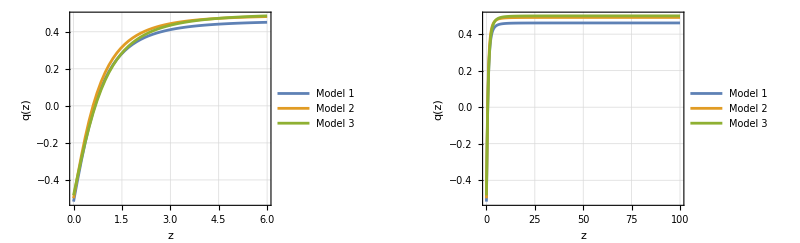

```mathematica
GraphicsRow[{
Plot[{qFn1a[z],qFn2a[z],qFn3a[z]},{z,0,zi},FrameLabel->{"z","q(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}]],
Plot[{qFn1a[z],qFn2a[z],qFn3a[z]},{z,0,zinitial},FrameLabel->{"z","q(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}]]},ImageSize->Full]
```

```mathematica
{qFn1a[zi],qFn2a[zi],qFn3a[zi]}
{qFn1a[zinitial],qFn2a[zinitial],qFn3a[zinitial]}
```

{0.451275,0.482098,0.485953}

{0.461237,0.491333,0.499992}

#### Integrating H(z)

```mathematica
SolveForH[H0val_?NumericQ,ϵval_?NumericQ,jModel_, qFn_]:=
Module[{odeH,sol},
odeH={dH/.q->qFn/.j->jModel/.ϵ->ϵval,H[0]==H0val};
sol=NDSolve[odeH,H,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
H/.sol[[1]]]
```

```mathematica
HFn1a=SolveForH[H01a,ϵ1a,j1, qFn1a];
HFn2a=SolveForH[H02a,ϵ2a,j2, qFn2a];
HFn3a=SolveForH[H03a,ϵ3a,j3, qFn3a];
```

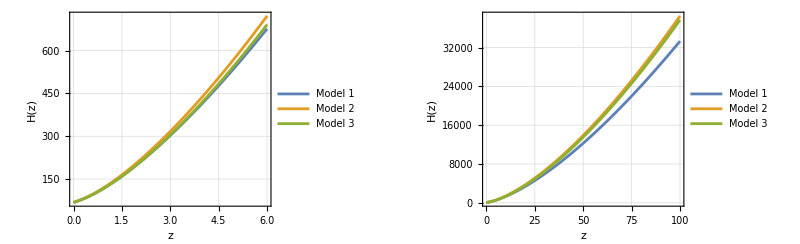

```mathematica
GraphicsRow[{
Plot[{HFn1a[z],HFn2a[z],HFn3a[z]},{z,0,zi},FrameLabel->{"z","H(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}]],
Plot[{HFn1a[z],HFn2a[z],HFn3a[z]},{z,0,zinitial},FrameLabel->{"z","H(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}]]},ImageSize->Full]
```

#### Integrating h(z)

```mathematica
SolveForh[H0val_?NumericQ,ϵval_?NumericQ,jModel_, qFn_]:=
Module[{odeH,sol},
odeH={dh/.q->qFn/.j->jModel/.ϵ->ϵval,h[0]==1};
sol=NDSolve[odeH,h,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
h/.sol[[1]]]
```

```mathematica
hFn1a=SolveForh[H01a,ϵ1a,j1, qFn1a];
hFn2a=SolveForh[H02a,ϵ2a,j2, qFn2a];
hFn3a=SolveForh[H03a,ϵ3a,j3, qFn3a];
```

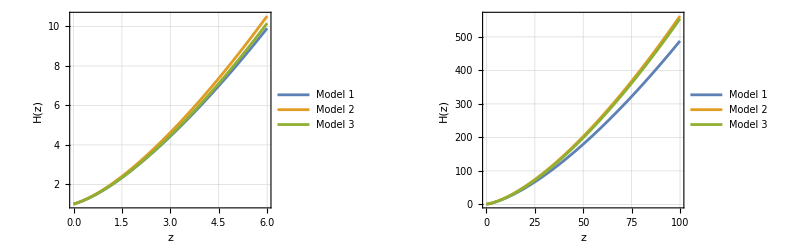

```mathematica
GraphicsRow[{
Plot[{hFn1a[z],hFn2a[z],hFn3a[z]},{z,0,zi},FrameLabel->{"z","H(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}]],
Plot[{hFn1a[z],hFn2a[z],hFn3a[z]},{z,0,zinitial},FrameLabel->{"z","H(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}]]},ImageSize->Full]
```

## Obtaining Background solution

#### Initial conditions

```mathematica
x0=-0.001;
Ω0=0.993243;
```

```mathematica
IC1a={zi,x0,Ω0,qFn1a[6]};
IC2a={zi,x0,Ω0,qFn2a[6]};
IC3a={zi,x0,Ω0,qFn3a[6]};
```

#### Module + models solutions

```mathematica
SolveBackground[jModel_,ICs_List, ϵVal_]:=
Module[{z0,x0,Ω0,q0,sExpr,lExpr,solFwd,solBwd, hsol, xFn, ΩFn, qFn, hFn},
{z0,x0,Ω0,q0}=ICs;

Block[{j,s,l, ϵ},
ϵ=ϵVal;

j[z_]=jModel;
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]/. q'[z]->Solve[dq,q'[z]][[1,1,2]]//Simplify;

(*Forward:z0->0*)
solFwd=NDSolve[{dx,dΩ,dq,x[z0]==x0,Ω[z0]==Ω0,q[z0]==q0},{x,Ω,q},{z,z0,0},PrecisionGoal->10, AccuracyGoal->10][[1]];
(*Backward:z0->zinitial*)
solBwd=NDSolve[{dx,dΩ,dq,x[z0]==x0,Ω[z0]==Ω0,q[z0]==q0},{x,Ω,q},{z,z0,zinitial},PrecisionGoal->10, AccuracyGoal->10][[1]];

xFn=With[{fwd=x/. solFwd,bwd=x/. solBwd,z0val=z0},Function[z,Piecewise[{{fwd[z],z<=z0val},{bwd[z],z>z0val}}]]];
ΩFn=With[{fwd=Ω/. solFwd,bwd=Ω/. solBwd,z0val=z0},Function[z,Piecewise[{{fwd[z],z<=z0val},{bwd[z],z>z0val}}]]];
];


<|"x"->xFn,"Ω"->ΩFn,"z0"->z0, "zinitial"->zinitial|>
];
```

```mathematica
sol1a=SolveBackground[j1[z],IC1a, ϵ1a];
replacements1a={x->sol1a["x"], Ω->sol1a["Ω"],q->qFn1a ,h->hFn1a,H->HFn1a, ϵ->ϵ1a,j->j1,Ωm0->Ωm01a,H0->H01a};
```

```mathematica
sol2a=SolveBackground[j2[z],IC2a, ϵ2a];
replacements2a={x->sol2a["x"], Ω->sol2a["Ω"],q->qFn2a ,h->hFn1a,H->HFn2a, ϵ->ϵ2a,j->j2,Ωm0->Ωm02a,H0->H02a};
```

```mathematica
sol3a=SolveBackground[j3[z],IC3a, ϵ3a];
replacements3a={x->sol3a["x"], Ω->sol3a["Ω"],q->qFn3a ,h->hFn1a,H->HFn3a, ϵ->ϵ3a,j->j3,Ωm0->Ωm03a,H0->H03a};
```

#### LCDM solution:

```mathematica
(* ΛCDM parameters *)
Ωm0LCDM=0.3;
hLCDM[z_]:= Sqrt[Ωm0LCDM(1+z)^3+(1-Ωm0LCDM)];
HLCDM[z_]=H0 hLCDM[z];
ΩΛ0=1-Ωm0LCDM;
```

```mathematica
qLCDM[z_]:=-1+(1+z)HLCDM'[z]/HLCDM[z];
```

```mathematica
xLCDM[z_]:=0 
ΩLCDM[z_]:= (Ωm0LCDM(1+z)^3)/(Ωm0LCDM(1+z)^3+ΩΛ0)
```

```mathematica
solLCDM=<|"x"->xLCDM[z],"Ω"->ΩLCDM[z],"q"->qLCDM[z],"h"->hLCDM[z],"z0"->z0|>;
LCDMreplacements={H[z]->HLCDM[z], h->hLCDM,q[z]->qLCDM[z], j[z]->1, x[z]->xLCDM[z], Ω[z]->ΩLCDM[z],Ωm0->Ωm0LCDM};
```

### Plotting x, Ω for all models

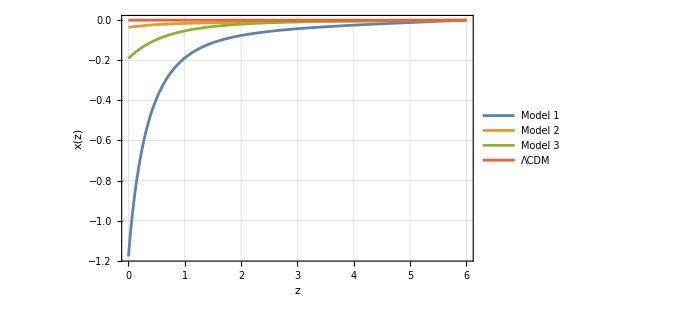

```mathematica
xplotCombined=Plot[
Evaluate[{sol1a["x"][z],sol2a["x"][z],sol3a["x"][z],xLCDM[z]}],{z,0,zi},
ImageSize->500,
Frame->True,FrameLabel->{"z","x(z)"}, GridLines->Automatic,
PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
```

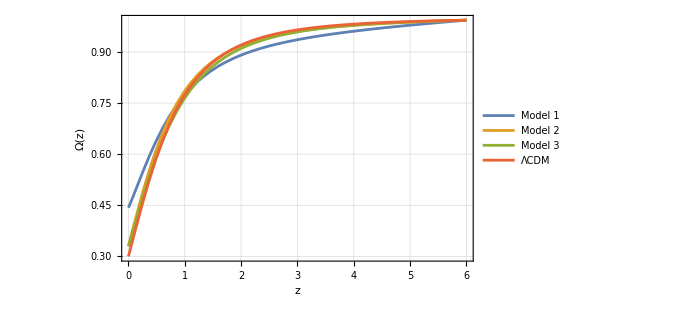

```mathematica
ΩplotCombined=Plot[
Evaluate[{sol1a["Ω"][z],sol2a["Ω"][z],sol3a["Ω"][z],ΩLCDM[z]}],{z,0,zi},
ImageSize->500,
Frame->True,FrameLabel->{"z","Ω(z)"}, GridLines->Automatic,
PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
```

```mathematica
{sol1a["Ω"][z],sol2a["Ω"][z],sol3a["Ω"][z], ΩLCDM[z]}/.z->0
```

{0.442852,0.32985,0.32987,0.3}

### Matter density (Ω_m) Analysis

```mathematica
Ωm[z_] :=Ωm0/h[z]^2(1+z)^3;
```

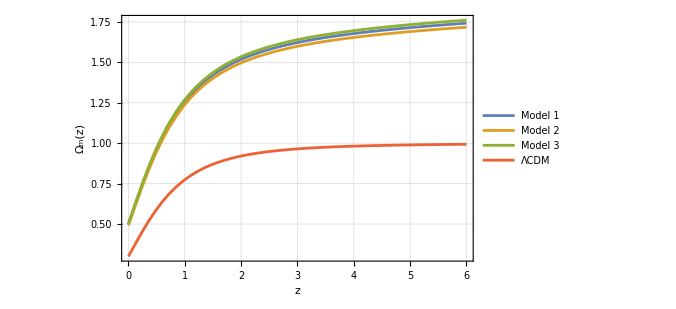

```mathematica
matterDensityCombined=Plot[Evaluate[
{Ωm[z]/. replacements1a,Ωm[z]/. replacements2a,Ωm[z]/. replacements3a,Ωm[z]/. LCDMreplacements}],
{z,0,zi},
ImageSize->500,GridLines->Automatic,
PlotRange->{{0,zi},Automatic},Frame->True,FrameLabel->{"z","Ω_m(z)"},PlotLegends->Placed[
LineLegend[{"Model 1", "Model 2", "Model 3", "ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.3}],
PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
```